# Project Beer

```mathematica
Share[]
```

1863288

## Input

```mathematica
SetDirectory["C:\\Users\\hilma\\OneDrive\\Documents\\Post Project\\MSTM\\MSTM-main\\pre"]
```

C:\Users\hilma\OneDrive\Documents\Post Project\MSTM\MSTM-main\pre

```mathematica
config[file_]:=Module[{f,dat,tpos,trad,p},
f=OpenRead[file];
dat=ReadList[f, Table[Number, {4}]];
tpos=Table[dat[[i,{1,2,3}]],{i,Length[dat]}];
trad=Table[dat[[i,4]],{i,Length[dat]}];
p=Table[Sphere[tpos[[i]],trad[[i]]],{i,Length[dat]}];
p];
oCount[tpos_,medp_]:=Module[{count},
count=Table[0,{i,8}];
Do[
If[(tpos[[i,1]]>medp[[1]])&&(tpos[[i,2]]>medp[[2]])&&(tpos[[i,3]]>medp[[3]]),count[[1]]=count[[1]]+1];
If[(tpos[[i,1]]<medp[[1]])&&(tpos[[i,2]]>medp[[2]])&&(tpos[[i,3]]>medp[[3]]),count[[2]]=count[[2]]+1];
If[(tpos[[i,1]]<medp[[1]])&&(tpos[[i,2]]<medp[[2]])&&(tpos[[i,3]]>medp[[3]]),count[[3]]=count[[3]]+1];
If[(tpos[[i,1]]>medp[[1]])&&(tpos[[i,2]]<medp[[2]])&&(tpos[[i,3]]>medp[[3]]),count[[4]]=count[[4]]+1];
If[(tpos[[i,1]]>medp[[1]])&&(tpos[[i,2]]>medp[[2]])&&(tpos[[i,3]]<medp[[3]]),count[[5]]=count[[5]]+1];
If[(tpos[[i,1]]<medp[[1]])&&(tpos[[i,2]]>medp[[2]])&&(tpos[[i,3]]<medp[[3]]),count[[6]]=count[[6]]+1];
If[(tpos[[i,1]]<medp[[1]])&&(tpos[[i,2]]<medp[[2]])&&(tpos[[i,3]]<medp[[3]]),count[[7]]=count[[7]]+1];
If[(tpos[[i,1]]>medp[[1]])&&(tpos[[i,2]]<medp[[2]])&&(tpos[[i,3]]<medp[[3]]),count[[8]]=count[[8]]+1];
,{i,Length[tpos]}];
count];
octAnalysis[file_]:=Module[{f,dat,tpos,trad,pmin,pmax,medp,sphere,octant,g,count},
f=OpenRead[file];
dat=ReadList[f, Table[Number, {4}]];
tpos=Table[dat[[i,{1,2,3}]],{i,Length[dat]}];
trad=Table[dat[[i,4]],{i,Length[dat]}];
pmin=Table[Min[tpos[[All,i]]]-trad[[1]],{i,3}];
pmax=Table[Max[tpos[[All,i]]]+trad[[1]],{i,3}];
medp=Table[0.5×(Min[tpos[[All,i]]]+Max[tpos[[All,i]]]),{i,3}];
sphere=Table[Sphere[tpos[[i]],trad[[i]]],{i,Length[dat]}];
octant={{Opacity[0.1],Cuboid[pmin,medp]},{Opacity[0.1],Cuboid[{medp[[1]],pmin[[2]],pmin[[3]]},{pmax[[1]],medp[[2]],medp[[3]]}]},{Opacity[0.1],Cuboid[{pmin[[1]],medp[[2]],pmin[[3]]},{medp[[1]],pmax[[2]],medp[[3]]}]},{Opacity[0.1],Cuboid[{medp[[1]],medp[[2]],pmin[[3]]},{pmax[[1]],pmax[[2]],medp[[3]]}]},{Opacity[0.1],Cuboid[{pmin[[1]],pmin[[2]],medp[[3]]},{medp[[1]],medp[[2]],pmax[[3]]}]},{Opacity[0.1],Cuboid[{medp[[1]],pmin[[2]],medp[[3]]},{pmax[[1]],medp[[2]],pmax[[3]]}]},{Opacity[0.1],Cuboid[{pmin[[1]],medp[[2]],medp[[3]]},{medp[[1]],pmax[[2]],pmax[[3]]}]},{Opacity[0.1],Cuboid[medp,pmax]}};
g=Graphics3D[{sphere,octant},Axes->True];
count=oCount[tpos,medp];
{g,count}];
pOctAnalysis[file_]:=Module[{f,dat,tpos,trad,pmin,pmax,medp,sphere,octant,g,count},
f=OpenRead[file];
dat=ReadList[f, Table[Number, {4}]];
tpos=Table[dat[[i,{1,2,3}]],{i,Length[dat]}];
trad=Table[dat[[i,4]],{i,Length[dat]}];
pmin=Table[Min[tpos[[All,i]]]-trad[[1]],{i,3}];
pmax=Table[Max[tpos[[All,i]]]+trad[[1]],{i,3}];
medp=Table[0.5×(Min[tpos[[All,i]]]+Max[tpos[[All,i]]]),{i,3}];
count=oCount[tpos,medp];
{tpos,trad,pmin,pmax,medp,count}];
```

## Concentration

Target radius = 1.5 μm, thickness = 0.6 μm; sphere radius = 0.1 μm

### Samples

#### Sphere number = 50

```mathematica
figN050=Graphics3D[config["beer_n_050_config.pos"],Axes->True]
```

-Graphics3D-

```mathematica
Animate[Graphics3D[config["beer_n_050_config.pos"],SphericalRegion->True,ViewVector->Dynamic[{{25*Cos@t,25*Sin@t,20},{0,0,0}},None],ViewVertical->{0,0,1},ViewAngle->Automatic],{t,0,2 Pi,.1},SaveDefinitions->True]
```

#### Sphere number = 100

```mathematica
figN100=Graphics3D[config["beer_n_100_config.pos"],Axes->True]
```

-Graphics3D-

```mathematica
Animate[Graphics3D[config["beer_n_100_config.pos"],SphericalRegion->True,ViewVector->Dynamic[{{25*Cos@t,25*Sin@t,20},{0,0,0}},None],ViewVertical->{0,0,1},ViewAngle->Automatic],{t,0,2 Pi,.1},SaveDefinitions->True]
```

#### Sphere number = 150

```mathematica
figN150=Graphics3D[config["beer_n_150_config.pos"],Axes->True]
```

-Graphics3D-

```mathematica
Animate[Graphics3D[config["beer_n_150_config.pos"],SphericalRegion->True,ViewVector->Dynamic[{{25*Cos@t,25*Sin@t,20},{0,0,0}},None],ViewVertical->{0,0,1},ViewAngle->Automatic],{t,0,2 Pi,.1},SaveDefinitions->True]
```

## Target dimension

Sphere number = 100, radius = 0.1 μm

### Samples

#### Target radius = 1.3 μm, thickness = 0.8 μm

```mathematica
figR13HT4=Graphics3D[config["beer_r_13_ht_4_config.pos"],Axes->True]
```

-Graphics3D-

```mathematica
Animate[Graphics3D[config["beer_r_13_ht_4_config.pos"],SphericalRegion->True,ViewVector->Dynamic[{{25*Cos@t,25*Sin@t,20},{0,0,0}},None],ViewVertical->{0,0,1},ViewAngle->Automatic],{t,0,2 Pi,.1},SaveDefinitions->True]
```

#### Target radius = 1.5 μm, thickness = 0.6 μm

```mathematica
figR15HT3=Graphics3D[config["beer_r_15_ht_3_config.pos"],Axes->True]
```

-Graphics3D-

```mathematica
Animate[Graphics3D[config["beer_r_15_ht_3_config.pos"],SphericalRegion->True,ViewVector->Dynamic[{{25*Cos@t,25*Sin@t,20},{0,0,0}},None],ViewVertical->{0,0,1},ViewAngle->Automatic],{t,0,2 Pi,.1},SaveDefinitions->True]
```

#### Target radius = 2.0 μm, thickness = 0.3375 μm

```mathematica
figR20HT1=Graphics3D[config["beer_r_20_ht_1.6875_config.pos"],Axes->True]
```

-Graphics3D-

```mathematica
Animate[Graphics3D[config["beer_r_20_ht_1.6875_config.pos"],SphericalRegion->True,ViewVector->Dynamic[{{25*Cos@t,25*Sin@t,20},{0,0,0}},None],ViewVertical->{0,0,1},ViewAngle->Automatic],{t,0,2 Pi,.1},SaveDefinitions->True]
```

## Random Configuration

Sphere number = 100, radius = 0.1 μm; target radius = 1.5 μm, thickness = 0.6 μm

### Configuration A

```mathematica
figCA=Graphics3D[config["beer_n_100_a_config.pos"],Axes->True]
```

-Graphics3D-

```mathematica
Animate[Graphics3D[config["beer_n_100_a_config.pos"],SphericalRegion->True,ViewVector->Dynamic[{{25*Cos@t,25*Sin@t,20},{0,0,0}},None],ViewVertical->{0,0,1},ViewAngle->Automatic],{t,0,2 Pi,.1},SaveDefinitions->True]
```

### Configuration B

```mathematica
figCB=Graphics3D[config["beer_n_100_b_config.pos"],Axes->True]
```

-Graphics3D-

```mathematica
Animate[Graphics3D[config["beer_n_100_b_config.pos"],SphericalRegion->True,ViewVector->Dynamic[{{25*Cos@t,25*Sin@t,20},{0,0,0}},None],ViewVertical->{0,0,1},ViewAngle->Automatic],{t,0,2 Pi,.1},SaveDefinitions->True]
```

### Configuration C

```mathematica
figCC=Graphics3D[config["beer_n_100_c_config.pos"],Axes->True]
```

-Graphics3D-

```mathematica
Animate[Graphics3D[config["beer_n_100_c_config.pos"],SphericalRegion->True,ViewVector->Dynamic[{{25*Cos@t,25*Sin@t,20},{0,0,0}},None],ViewVertical->{0,0,1},ViewAngle->Automatic],{t,0,2 Pi,.1},SaveDefinitions->True]
```

## Distinct Configuration

Sphere number = 100, radius = 0.1 μm; target shape = cuboid, dimension = 3.2 × 3 × 0.8 μm^3
Octant type description in cuboid:
-Graphics-

### Configuration 1

```mathematica
{tpos,trad,pmin,pmax,medp,count}=pOctAnalysis["beer_1_config.pos"];
sphere1=Table[Sphere[tpos[[i]],trad[[i]]],{i,Length[trad]}];
octant1={{Opacity[0.1],Cuboid[pmin,medp]},{Opacity[0.1],Cuboid[{medp[[1]],pmin[[2]],pmin[[3]]},{pmax[[1]],medp[[2]],medp[[3]]}]},{Opacity[0.1],Cuboid[{pmin[[1]],medp[[2]],pmin[[3]]},{medp[[1]],pmax[[2]],medp[[3]]}]},{Opacity[0.1],Cuboid[{medp[[1]],medp[[2]],pmin[[3]]},{pmax[[1]],pmax[[2]],medp[[3]]}]},{Opacity[0.1],Cuboid[{pmin[[1]],pmin[[2]],medp[[3]]},{medp[[1]],medp[[2]],pmax[[3]]}]},{Opacity[0.1],Cuboid[{medp[[1]],pmin[[2]],medp[[3]]},{pmax[[1]],medp[[2]],pmax[[3]]}]},{Opacity[0.1],Cuboid[{pmin[[1]],medp[[2]],medp[[3]]},{medp[[1]],pmax[[2]],pmax[[3]]}]},{Opacity[0.1],Cuboid[medp,pmax]}};
Graphics3D[{sphere1,octant1},Axes->True]
Animate[Graphics3D[{sphere1,octant1},SphericalRegion->True,ViewVector->Dynamic[{{50*Cos@t,50*Sin@t,10},{0,0,0}},None],ViewVertical->{0,0,1},ViewAngle->Automatic],{t,0,2 Pi,.1},SaveDefinitions->True]
Do[Print["Octant "<>ToString[i]<>" sphere number = "<>ToString[count[[i]]]],{i,Length[count]}]
```

-Graphics3D-

Octant 1 sphere number = 13

Octant 2 sphere number = 12

Octant 3 sphere number = 13

Octant 4 sphere number = 12

Octant 5 sphere number = 13

Octant 6 sphere number = 11

Octant 7 sphere number = 14

Octant 8 sphere number = 12

### Configuration 2

```mathematica
{tpos,trad,pmin,pmax,medp,count}=pOctAnalysis["beer_2_config.pos"];
sphere2=Table[Sphere[tpos[[i]],trad[[i]]],{i,Length[trad]}];
octant2={{Opacity[0.1],Cuboid[pmin,medp]},{Opacity[0.1],Cuboid[{medp[[1]],pmin[[2]],pmin[[3]]},{pmax[[1]],medp[[2]],medp[[3]]}]},{Opacity[0.1],Cuboid[{pmin[[1]],medp[[2]],pmin[[3]]},{medp[[1]],pmax[[2]],medp[[3]]}]},{Opacity[0.1],Cuboid[{medp[[1]],medp[[2]],pmin[[3]]},{pmax[[1]],pmax[[2]],medp[[3]]}]},{Opacity[0.3],Cuboid[{pmin[[1]],pmin[[2]],medp[[3]]},{medp[[1]],medp[[2]],pmax[[3]]}]},{Opacity[0.3],Cuboid[{medp[[1]],pmin[[2]],medp[[3]]},{pmax[[1]],medp[[2]],pmax[[3]]}]},{Opacity[0.3],Cuboid[{pmin[[1]],medp[[2]],medp[[3]]},{medp[[1]],pmax[[2]],pmax[[3]]}]},{Opacity[0.3],Cuboid[medp,pmax]}};
Graphics3D[{sphere2,octant2},Axes->True]
Animate[Graphics3D[{sphere2,octant2},SphericalRegion->True,ViewVector->Dynamic[{{50*Cos@t,50*Sin@t,10},{0,0,0}},None],ViewVertical->{0,0,1},ViewAngle->Automatic],{t,0,2 Pi,.1},SaveDefinitions->True]
Do[Print["Octant "<>ToString[i]<>" sphere number = "<>ToString[count[[i]]]],{i,Length[count]}]
```

-Graphics3D-

Octant 1 sphere number = 20

Octant 2 sphere number = 18

Octant 3 sphere number = 22

Octant 4 sphere number = 20

Octant 5 sphere number = 6

Octant 6 sphere number = 5

Octant 7 sphere number = 5

Octant 8 sphere number = 4

### Configuration 3

```mathematica
{tpos,trad,pmin,pmax,medp,count}=pOctAnalysis["beer_3_config.pos"];
sphere3=Table[Sphere[tpos[[i]],trad[[i]]],{i,Length[trad]}];
octant3={{Opacity[0.3],Cuboid[pmin,medp]},{Opacity[0.3],Cuboid[{medp[[1]],pmin[[2]],pmin[[3]]},{pmax[[1]],medp[[2]],medp[[3]]}]},{Opacity[0.3],Cuboid[{pmin[[1]],medp[[2]],pmin[[3]]},{medp[[1]],pmax[[2]],medp[[3]]}]},{Opacity[0.3],Cuboid[{medp[[1]],medp[[2]],pmin[[3]]},{pmax[[1]],pmax[[2]],medp[[3]]}]},{Opacity[0.1],Cuboid[{pmin[[1]],pmin[[2]],medp[[3]]},{medp[[1]],medp[[2]],pmax[[3]]}]},{Opacity[0.1],Cuboid[{medp[[1]],pmin[[2]],medp[[3]]},{pmax[[1]],medp[[2]],pmax[[3]]}]},{Opacity[0.1],Cuboid[{pmin[[1]],medp[[2]],medp[[3]]},{medp[[1]],pmax[[2]],pmax[[3]]}]},{Opacity[0.1],Cuboid[medp,pmax]}};
Graphics3D[{sphere3,octant3},Axes->True]
Animate[Graphics3D[{sphere3,octant3},SphericalRegion->True,ViewVector->Dynamic[{{50*Cos@t,50*Sin@t,10},{0,0,0}},None],ViewVertical->{0,0,1},ViewAngle->Automatic],{t,0,2 Pi,.1},SaveDefinitions->True]
Do[Print["Octant "<>ToString[i]<>" sphere number = "<>ToString[count[[i]]]],{i,Length[count]}]
```

-Graphics3D-

Octant 1 sphere number = 6

Octant 2 sphere number = 5

Octant 3 sphere number = 5

Octant 4 sphere number = 4

Octant 5 sphere number = 20

Octant 6 sphere number = 18

Octant 7 sphere number = 22

Octant 8 sphere number = 20

### Configuration 4

```mathematica
{tpos,trad,pmin,pmax,medp,count}=pOctAnalysis["beer_4_config.pos"];
sphere4=Table[Sphere[tpos[[i]],trad[[i]]],{i,Length[trad]}];
octant4={{Opacity[0.1],Cuboid[pmin,medp]},{Opacity[0.3],Cuboid[{medp[[1]],pmin[[2]],pmin[[3]]},{pmax[[1]],medp[[2]],medp[[3]]}]},{Opacity[0.1],Cuboid[{pmin[[1]],medp[[2]],pmin[[3]]},{medp[[1]],pmax[[2]],medp[[3]]}]},{Opacity[0.3],Cuboid[{medp[[1]],medp[[2]],pmin[[3]]},{pmax[[1]],pmax[[2]],medp[[3]]}]},{Opacity[0.1],Cuboid[{pmin[[1]],pmin[[2]],medp[[3]]},{medp[[1]],medp[[2]],pmax[[3]]}]},{Opacity[0.3],Cuboid[{medp[[1]],pmin[[2]],medp[[3]]},{pmax[[1]],medp[[2]],pmax[[3]]}]},{Opacity[0.1],Cuboid[{pmin[[1]],medp[[2]],medp[[3]]},{medp[[1]],pmax[[2]],pmax[[3]]}]},{Opacity[0.3],Cuboid[medp,pmax]}};
Graphics3D[{sphere4,octant4},Axes->True]
Animate[Graphics3D[{sphere4,octant4},SphericalRegion->True,ViewVector->Dynamic[{{50*Cos@t,50*Sin@t,10},{0,0,0}},None],ViewVertical->{0,0,1},ViewAngle->Automatic],{t,0,2 Pi,.1},SaveDefinitions->True]
Do[Print["Octant "<>ToString[i]<>" sphere number = "<>ToString[count[[i]]]],{i,Length[count]}]
```

-Graphics3D-

Octant 1 sphere number = 20

Octant 2 sphere number = 6

Octant 3 sphere number = 4

Octant 4 sphere number = 20

Octant 5 sphere number = 18

Octant 6 sphere number = 5

Octant 7 sphere number = 5

Octant 8 sphere number = 22

### Configuration 5

```mathematica
{tpos,trad,pmin,pmax,medp,count}=pOctAnalysis["beer_5_config.pos"];
sphere5=Table[Sphere[tpos[[i]],trad[[i]]],{i,Length[trad]}];
octant5={{Opacity[0.3],Cuboid[pmin,medp]},{Opacity[0.1],Cuboid[{medp[[1]],pmin[[2]],pmin[[3]]},{pmax[[1]],medp[[2]],medp[[3]]}]},{Opacity[0.3],Cuboid[{pmin[[1]],medp[[2]],pmin[[3]]},{medp[[1]],pmax[[2]],medp[[3]]}]},{Opacity[0.1],Cuboid[{medp[[1]],medp[[2]],pmin[[3]]},{pmax[[1]],pmax[[2]],medp[[3]]}]},{Opacity[0.3],Cuboid[{pmin[[1]],pmin[[2]],medp[[3]]},{medp[[1]],medp[[2]],pmax[[3]]}]},{Opacity[0.1],Cuboid[{medp[[1]],pmin[[2]],medp[[3]]},{pmax[[1]],medp[[2]],pmax[[3]]}]},{Opacity[0.3],Cuboid[{pmin[[1]],medp[[2]],medp[[3]]},{medp[[1]],pmax[[2]],pmax[[3]]}]},{Opacity[0.1],Cuboid[medp,pmax]}};
Graphics3D[{sphere5,octant5},Axes->True]
Animate[Graphics3D[{sphere5,octant5},SphericalRegion->True,ViewVector->Dynamic[{{50*Cos@t,50*Sin@t,10},{0,0,0}},None],ViewVertical->{0,0,1},ViewAngle->Automatic],{t,0,2 Pi,.1},SaveDefinitions->True]
Do[Print["Octant "<>ToString[i]<>" sphere number = "<>ToString[count[[i]]]],{i,Length[count]}]
```

-Graphics3D-

Octant 1 sphere number = 6

Octant 2 sphere number = 20

Octant 3 sphere number = 20

Octant 4 sphere number = 4

Octant 5 sphere number = 5

Octant 6 sphere number = 18

Octant 7 sphere number = 22

Octant 8 sphere number = 5

### Configuration 6

```mathematica
{tpos,trad,pmin,pmax,medp,count}=pOctAnalysis["beer_6_config.pos"];
sphere6=Table[Sphere[tpos[[i]],trad[[i]]],{i,Length[trad]}];
octant6={{Opacity[0.1],Cuboid[pmin,medp]},{Opacity[0.1],Cuboid[{medp[[1]],pmin[[2]],pmin[[3]]},{pmax[[1]],medp[[2]],medp[[3]]}]},{Opacity[0.1],Cuboid[{pmin[[1]],medp[[2]],pmin[[3]]},{medp[[1]],pmax[[2]],medp[[3]]}]},{Opacity[0.1],Cuboid[{medp[[1]],medp[[2]],pmin[[3]]},{pmax[[1]],pmax[[2]],medp[[3]]}]},{Opacity[0.1],Cuboid[{pmin[[1]],pmin[[2]],medp[[3]]},{medp[[1]],medp[[2]],pmax[[3]]}]},{Opacity[0.3],Cuboid[{medp[[1]],pmin[[2]],medp[[3]]},{pmax[[1]],medp[[2]],pmax[[3]]}]},{Opacity[0.1],Cuboid[{pmin[[1]],medp[[2]],medp[[3]]},{medp[[1]],pmax[[2]],pmax[[3]]}]},{Opacity[0.3],Cuboid[medp,pmax]}};
Graphics3D[{sphere6,octant6},Axes->True]
Animate[Graphics3D[{sphere6,octant6},SphericalRegion->True,ViewVector->Dynamic[{{50*Cos@t,50*Sin@t,10},{0,0,0}},None],ViewVertical->{0,0,1},ViewAngle->Automatic],{t,0,2 Pi,.1},SaveDefinitions->True]
Do[Print["Octant "<>ToString[i]<>" sphere number = "<>ToString[count[[i]]]],{i,Length[count]}]
```

-Graphics3D-

Octant 1 sphere number = 33

Octant 2 sphere number = 6

Octant 3 sphere number = 4

Octant 4 sphere number = 37

Octant 5 sphere number = 5

Octant 6 sphere number = 5

Octant 7 sphere number = 5

Octant 8 sphere number = 5

### Configuration 7

```mathematica
{tpos,trad,pmin,pmax,medp,count}=pOctAnalysis["beer_7_config.pos"];
sphere7=Table[Sphere[tpos[[i]],trad[[i]]],{i,Length[trad]}];
octant7={{Opacity[0.1],Cuboid[pmin,medp]},{Opacity[0.1],Cuboid[{medp[[1]],pmin[[2]],pmin[[3]]},{pmax[[1]],medp[[2]],medp[[3]]}]},{Opacity[0.1],Cuboid[{pmin[[1]],medp[[2]],pmin[[3]]},{medp[[1]],pmax[[2]],medp[[3]]}]},{Opacity[0.1],Cuboid[{medp[[1]],medp[[2]],pmin[[3]]},{pmax[[1]],pmax[[2]],medp[[3]]}]},{Opacity[0.3],Cuboid[{pmin[[1]],pmin[[2]],medp[[3]]},{medp[[1]],medp[[2]],pmax[[3]]}]},{Opacity[0.1],Cuboid[{medp[[1]],pmin[[2]],medp[[3]]},{pmax[[1]],medp[[2]],pmax[[3]]}]},{Opacity[0.3],Cuboid[{pmin[[1]],medp[[2]],medp[[3]]},{medp[[1]],pmax[[2]],pmax[[3]]}]},{Opacity[0.1],Cuboid[medp,pmax]}};
Graphics3D[{sphere7,octant7},Axes->True]
Animate[Graphics3D[{sphere7,octant7},SphericalRegion->True,ViewVector->Dynamic[{{50*Cos@t,50*Sin@t,10},{0,0,0}},None],ViewVertical->{0,0,1},ViewAngle->Automatic],{t,0,2 Pi,.1},SaveDefinitions->True]
Do[Print["Octant "<>ToString[i]<>" sphere number = "<>ToString[count[[i]]]],{i,Length[count]}]
```

-Graphics3D-

Octant 1 sphere number = 6

Octant 2 sphere number = 33

Octant 3 sphere number = 37

Octant 4 sphere number = 4

Octant 5 sphere number = 5

Octant 6 sphere number = 5

Octant 7 sphere number = 5

Octant 8 sphere number = 5

### Configuration 8

```mathematica
{tpos,trad,pmin,pmax,medp,count}=pOctAnalysis["beer_8_config.pos"];
sphere8=Table[Sphere[tpos[[i]],trad[[i]]],{i,Length[trad]}];
octant8={{Opacity[0.1],Cuboid[pmin,medp]},{Opacity[0.3],Cuboid[{medp[[1]],pmin[[2]],pmin[[3]]},{pmax[[1]],medp[[2]],medp[[3]]}]},{Opacity[0.1],Cuboid[{pmin[[1]],medp[[2]],pmin[[3]]},{medp[[1]],pmax[[2]],medp[[3]]}]},{Opacity[0.3],Cuboid[{medp[[1]],medp[[2]],pmin[[3]]},{pmax[[1]],pmax[[2]],medp[[3]]}]},{Opacity[0.1],Cuboid[{pmin[[1]],pmin[[2]],medp[[3]]},{medp[[1]],medp[[2]],pmax[[3]]}]},{Opacity[0.1],Cuboid[{medp[[1]],pmin[[2]],medp[[3]]},{pmax[[1]],medp[[2]],pmax[[3]]}]},{Opacity[0.1],Cuboid[{pmin[[1]],medp[[2]],medp[[3]]},{medp[[1]],pmax[[2]],pmax[[3]]}]},{Opacity[0.1],Cuboid[medp,pmax]}};
Graphics3D[{sphere8,octant8},Axes->True]
Animate[Graphics3D[{sphere8,octant8},SphericalRegion->True,ViewVector->Dynamic[{{50*Cos@t,50*Sin@t,10},{0,0,0}},None],ViewVertical->{0,0,1},ViewAngle->Automatic],{t,0,2 Pi,.1},SaveDefinitions->True]
Do[Print["Octant "<>ToString[i]<>" sphere number = "<>ToString[count[[i]]]],{i,Length[count]}]
```

-Graphics3D-

Octant 1 sphere number = 6

Octant 2 sphere number = 5

Octant 3 sphere number = 5

Octant 4 sphere number = 4

Octant 5 sphere number = 33

Octant 6 sphere number = 5

Octant 7 sphere number = 5

Octant 8 sphere number = 37

### Configuration 9

```mathematica
{tpos,trad,pmin,pmax,medp,count}=pOctAnalysis["beer_9_config.pos"];
sphere9=Table[Sphere[tpos[[i]],trad[[i]]],{i,Length[trad]}];
octant9={{Opacity[0.3],Cuboid[pmin,medp]},{Opacity[0.1],Cuboid[{medp[[1]],pmin[[2]],pmin[[3]]},{pmax[[1]],medp[[2]],medp[[3]]}]},{Opacity[0.3],Cuboid[{pmin[[1]],medp[[2]],pmin[[3]]},{medp[[1]],pmax[[2]],medp[[3]]}]},{Opacity[0.1],Cuboid[{medp[[1]],medp[[2]],pmin[[3]]},{pmax[[1]],pmax[[2]],medp[[3]]}]},{Opacity[0.1],Cuboid[{pmin[[1]],pmin[[2]],medp[[3]]},{medp[[1]],medp[[2]],pmax[[3]]}]},{Opacity[0.1],Cuboid[{medp[[1]],pmin[[2]],medp[[3]]},{pmax[[1]],medp[[2]],pmax[[3]]}]},{Opacity[0.1],Cuboid[{pmin[[1]],medp[[2]],medp[[3]]},{medp[[1]],pmax[[2]],pmax[[3]]}]},{Opacity[0.1],Cuboid[medp,pmax]}};
Graphics3D[{sphere9,octant9},Axes->True]
Animate[Graphics3D[{sphere9,octant9},SphericalRegion->True,ViewVector->Dynamic[{{50*Cos@t,50*Sin@t,10},{0,0,0}},None],ViewVertical->{0,0,1},ViewAngle->Automatic],{t,0,2 Pi,.1},SaveDefinitions->True]
Do[Print["Octant "<>ToString[i]<>" sphere number = "<>ToString[count[[i]]]],{i,Length[count]}]
```

-Graphics3D-

Octant 1 sphere number = 6

Octant 2 sphere number = 5

Octant 3 sphere number = 5

Octant 4 sphere number = 4

Octant 5 sphere number = 5

Octant 6 sphere number = 33

Octant 7 sphere number = 37

Octant 8 sphere number = 5

## Output

```mathematica
SetDirectory["C:\\Users\\hilma\\OneDrive\\Documents\\Post Project\\MSTM\\MSTM-main\\post"]
```

C:\Users\hilma\OneDrive\Documents\Post Project\MSTM\MSTM-main\post

```mathematica
nfread[file_]:=Module[{f,dat,sdat,pos,n,c,cdim,tdat,gmin,gmax,nb,bdat},f=OpenRead[file];
tdat={};
Do[
pos=Find[f," run number"];
If[ToString[pos]=="EndOfFile",Break[]];
n=Read[f,Number];
n=Read[f,Number];
If[n>0,c=ReadList[f,Table[Number,{4}],n],c={}];
sdat={n,c};
n=Read[f,Number];
If[n>0,c=ReadList[f,Number,n],c={}];
bdat={n,c};
gmin=Read[f,Table[Number,{3}]];
gmax=Read[f,Table[Number,{3}]];
cdim=Read[f,Table[Number,{3}]];
n=cdim[[1]]cdim[[2]]cdim[[3]];
dat=ReadList[f,Table[Number,{27}],n];
tdat=Append[tdat,{cdim,{gmin,gmax},sdat,bdat,dat}];
,{i,1,1000}];
Close[f];
tdat]
cplot[tdat_]:=Module[{cdim,rmin,rmax,splot,nb,bplot,ep,b,arat},
cdim=tdat[[1]];
p=Which[cdim[[1]]==1,1,cdim[[2]]==1,2,cdim[[3]]==1,3];
rmin=Drop[tdat[[2,1]],{p}];rmax=Drop[tdat[[2,2]],{p}];
ppos=tdat[[2,1,p]];
ns=tdat[[3,1]];sdat=tdat[[3,2]];
nis=0;ispos={};israd={};
Do[
t1=Abs[sdat[[i,p]]-ppos];
If[t1<sdat[[i,4]],
nis=nis+1;
ispos=Append[ispos,Drop[sdat[[i,{1,2,3}]],{p}]];
israd=Append[israd,Sqrt[sdat[[i,4]]^2-t1^2]];
];
,
{i,1,ns}];
splot=Table[Circle[ispos[[i]],israd[[i]]],{i,1,nis}];
nb=tdat[[4 ,1]];b=tdat[[4,2]];
bplot=If[nb>0,Table[Line[{{rmin[[1]],b[[i]]},{rmax[[1]],b[[i]]}}],{i,1,nb}],{}];
ep=Epilog->{splot,bplot};
arat=AspectRatio->Which[p==1,cdim[[3]]/cdim[[2]],p==2,cdim[[3]]/cdim[[1]],p==3,cdim[[2]]/cdim[[1]]];
{ep,arat}]
readmstm[file_,vars_,len_]:=Module[{f,newlist,str,dat,pos,tdat,t1},
f=OpenRead[file];
newlist=" input variables";
str=Find[f,newlist];
dat={};
Do[
pos=StreamPosition[f];
tdat=Table[Null[],{Length[vars]}];
Do[
str=ToString[Find[f,{newlist,vars[[j]]}]];
If[str==ToString[EndOfFile],Break[]];
If[Length[StringCases[str,vars[[j]]]]!=0,
t1=Read[f,Table[Number,{len[[j]]}]][[len[[j]]]];
tdat[[j]]=t1;
];
SetStreamPosition[f,pos];
,{j,1,Length[vars]}];
dat=Append[dat,tdat];
str=ToString[Find[f,newlist]];
If[str==ToString[EndOfFile],Break[]];
,{i,1,100000}];
Close[f];
dat]
readsmt[file_,sme_]:=Module[{f,tn,datsm,sm},
f=OpenRead[file];
Find[f,"number directions, number"];
tn=Read[f,Table[Number,{2}]];
Find[f,"  theta     11"];
datsm=ReadList[f, Table[Number, {tn[[2]]+1}],tn[[1]]];
sm=Table[datsm[[i,{1,sme}]],{i,Length[datsm]}];
Close[f];
sm]
calcsmr[sm1_,sm2_,val_]:=Module[{sm},
sm=RandomInteger[1,{Length[sm1],2}];
sm[[All,1]]=sm1[[All,1]];
sm[[All,2]]=sm2[[All,2]]/sm1[[All,2]];
If[val==1,
sm[[All,2]]=-sm[[All,2]]];
sm]
readap[file_]:=Module[{f,newlist,str,alpha11,tap,ap},
f=OpenRead[file];
newlist="    n       11          12";
ap={};
Do[str=ToString[Find[f,newlist]];
If[str==ToString[EndOfFile],Break[]];
ReadLine[f];
alpha11=Read[f,Table[Number,{2}]][[2]];
tap=alpha11/3;
ap=Append[ap,tap];,100000];
Close[f];
ap]
```

```mathematica
vars={" length, ref index"," unit cell reflectance"," unit cell reflectance"," unit cell reflectance"," unit cell reflectance"," unit cell reflectance"," unit cell reflectance"," unit cell reflectance"," unit cell reflectance"," unit cell reflectance"};
len={1,4,7,1,5,8,2,6,9,3};
datN050=readmstm["beer_n_050_var.dat",vars,len];
datN100=readmstm["beer_n_100_var.dat",vars,len];
datN150=readmstm["beer_n_150_var.dat",vars,len];
datR13HT4=readmstm["beer_r_13_ht_4_var.dat",vars,len];
datR15HT3=readmstm["beer_r_15_ht_3_var.dat",vars,len];
datR20HT1=readmstm["beer_r_20_ht_1.6875_var.dat",vars,len];
datCA=readmstm["beer_n_100_a_var.dat",vars,len];
datCB=readmstm["beer_n_100_b_var.dat",vars,len];
datCC=readmstm["beer_n_100_c_var.dat",vars,len];
datPN=readmstm["beer_pyramid_norm_var.dat",vars,len];
datPI=readmstm["beer_pyramid_inv_var.dat",vars,len];
dat={datN050,datN100,datN150,datR13HT4,datR15HT3,datR20HT1,datCA,datCB,datCC,datPN,datPI};
wav=(2 Pi)/datN050[[All,1]] 0.1 ×1000;
```

## Concentration

### Reflectance

```mathematica
g=Table[ListLogPlot[Table[{wav[[j]],dat[[i,j,k]]},{i,1,3},{j,1,Length[wav]}],PlotStyle->Table[ColorData[97,i],{i,3}], Frame->True,Axes->False,FrameStyle->Medium,Joined->True,AspectRatio->1,FrameLabel->{"wavelength (nm)","reflectance"},PlotRangePadding->None],{k,2,4}];
```

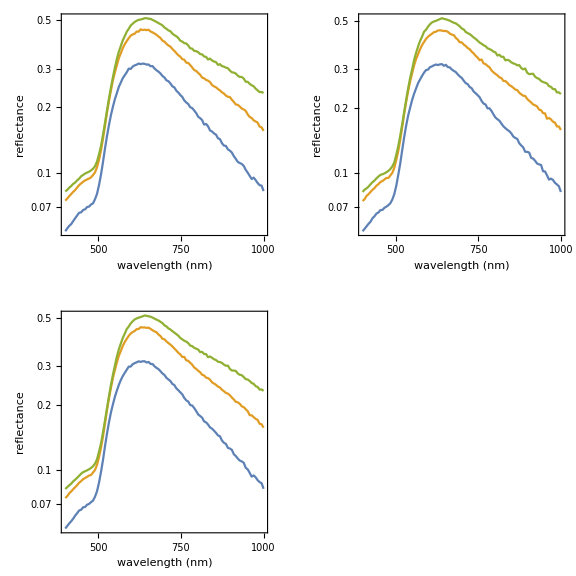

```mathematica
g2=Legended[GraphicsGrid[{{g[[1]],g[[2]]},{g[[3]]}},ImageSize->Large],Placed[LineLegend[Table[ColorData[97,i],{i,3}],{"50 spheres","100 spheres","150 spheres"},LabelStyle->{13,White}],{0.99,0.1}]]
```

top left to right: E_(||), E_⊥
bottom left: unpolarized incident EM

### Absorptance

```mathematica
g=Table[ListLogPlot[Table[{wav[[j]],dat[[i,j,k]]},{i,1,3},{j,1,Length[wav]}],PlotStyle->Table[ColorData[97,i],{i,3}], Frame->True,Axes->False,FrameStyle->Medium,Joined->True,AspectRatio->1,FrameLabel->{"wavelength (nm)","absorptance"},PlotRangePadding->None],{k,5,7}];
```

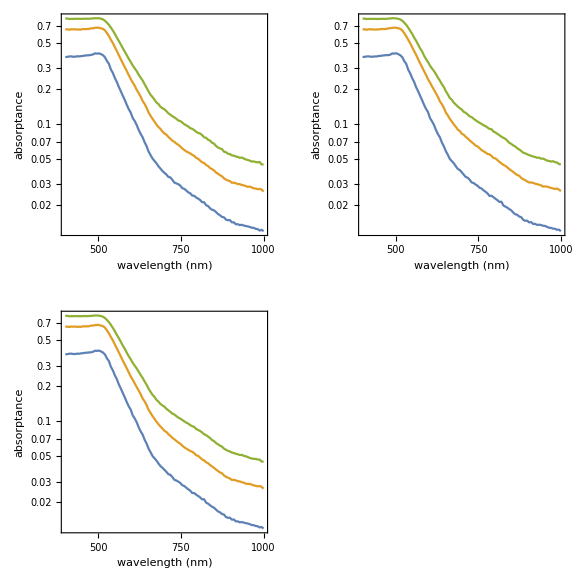

```mathematica
g2=Legended[GraphicsGrid[{{g[[1]],g[[2]]},{g[[3]]}},ImageSize->Large],Placed[LineLegend[Table[ColorData[97,i],{i,3}],{"50 spheres","100 spheres","150 spheres"},LabelStyle->{13,White}],{0.99,0.1}]]
```

top left to right: E_(||), E_⊥
bottom left: unpolarized incident EM

### Transmittance

```mathematica
g=Table[ListLogPlot[Table[{wav[[j]],dat[[i,j,k]]},{i,1,3},{j,1,Length[wav]}],PlotStyle->Table[ColorData[97,i],{i,3}], Frame->True,Axes->False,FrameStyle->Medium,Joined->True,AspectRatio->1,FrameLabel->{"wavelength (nm)","transmittance"},PlotRangePadding->None],{k,8,10}];
```

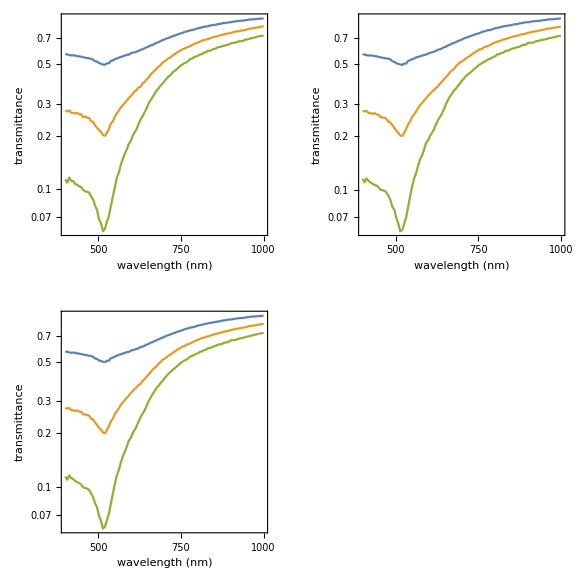

```mathematica
g2=Legended[GraphicsGrid[{{g[[1]],g[[2]]},{g[[3]]}},ImageSize->Large],Placed[LineLegend[Table[ColorData[97,i],{i,3}],{"50 spheres","100 spheres","150 spheres"},LabelStyle->{13,White}],{0.99,0.1}]]
```

top left to right: E_(||), E_⊥
bottom left: unpolarized incident EM

### Absorbance

```mathematica
data=dat;
Do[data[[All,All,i]]=-Log[10,dat[[All,All,i]]],{i,8,10}];
g=Table[ListPlot[Table[{wav[[j]],data[[i,j,k]]},{i,1,3},{j,1,Length[wav]}],PlotStyle->Table[ColorData[97,i],{i,3}], Frame->True,Axes->False,FrameStyle->Medium,Joined->True,AspectRatio->1,FrameLabel->{"wavelength (nm)","absorbance"},PlotRangePadding->None],{k,8,10}];
```

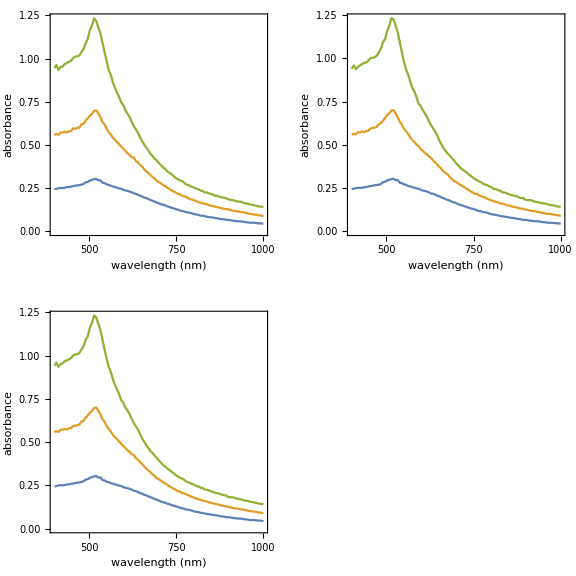

```mathematica
g2=Legended[GraphicsGrid[{{g[[1]],g[[2]]},{g[[3]]}},ImageSize->Large],Placed[LineLegend[Table[ColorData[97,i],{i,3}],{"50 spheres","100 spheres","150 spheres"},LabelStyle->{13,White}],{0.99,0.1}]]
```

top left to right: E_(||), E_⊥
bottom left: unpolarized incident EM

## Target dimension

### Reflectance

```mathematica
g=Table[ListLogPlot[Table[{wav[[j]],dat[[i,j,k]]},{i,4,6},{j,1,Length[wav]}],PlotStyle->Table[ColorData[97,i],{i,3}], Frame->True,Axes->False,FrameStyle->Medium,Joined->True,AspectRatio->1,FrameLabel->{"wavelength (nm)","reflectance"},PlotRangePadding->None],{k,2,4}];
```

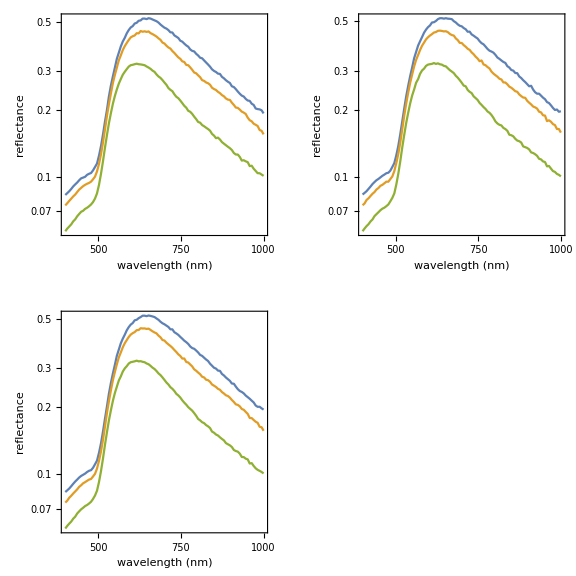

```mathematica
g2=Legended[GraphicsGrid[{{g[[1]],g[[2]]},{g[[3]]}},ImageSize->Large],Placed[LineLegend[Table[ColorData[97,i],{i,3}],{"Target radius = 1.3 μm, thickness = 0.8 μm","Target radius = 1.5 μm, thickness = 0.6 μm","Target radius = 2.0 μm, thickness = 0.3375 μm"},LabelStyle->{13,White}],{0.99,0.1}]]
```

top left to right: E_(||), E_⊥
bottom left: unpolarized incident EM

### Absorptance

```mathematica
g=Table[ListLogPlot[Table[{wav[[j]],dat[[i,j,k]]},{i,4,6},{j,1,Length[wav]}],PlotStyle->Table[ColorData[97,i],{i,3}], Frame->True,Axes->False,FrameStyle->Medium,Joined->True,AspectRatio->1,FrameLabel->{"wavelength (nm)","absorptance"},PlotRangePadding->None],{k,5,7}];
```

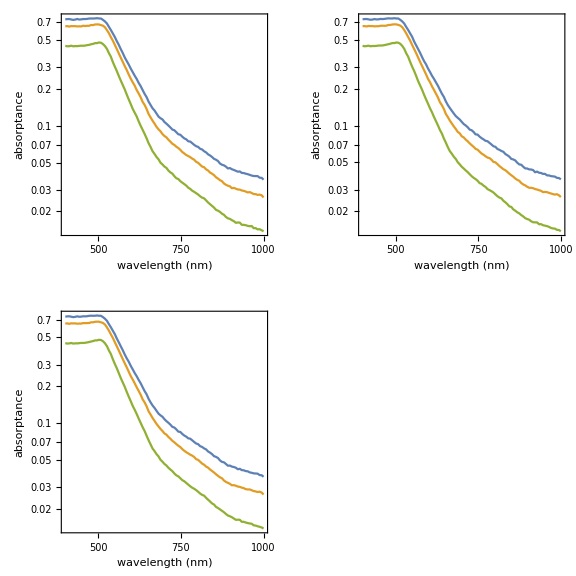

```mathematica
g2=Legended[GraphicsGrid[{{g[[1]],g[[2]]},{g[[3]]}},ImageSize->Large],Placed[LineLegend[Table[ColorData[97,i],{i,3}],{"Target radius = 1.3 μm, thickness = 0.8 μm","Target radius = 1.5 μm, thickness = 0.6 μm","Target radius = 2.0 μm, thickness = 0.3375 μm"},LabelStyle->{13,White}],{0.99,0.1}]]
```

top left to right: E_(||), E_⊥
bottom left: unpolarized incident EM

### Transmittance

```mathematica
g=Table[ListLogPlot[Table[{wav[[j]],dat[[i,j,k]]},{i,4,6},{j,1,Length[wav]}],PlotStyle->Table[ColorData[97,i],{i,3}], Frame->True,Axes->False,FrameStyle->Medium,Joined->True,AspectRatio->1,FrameLabel->{"wavelength (nm)","transmittance"},PlotRangePadding->None],{k,8,10}];
```

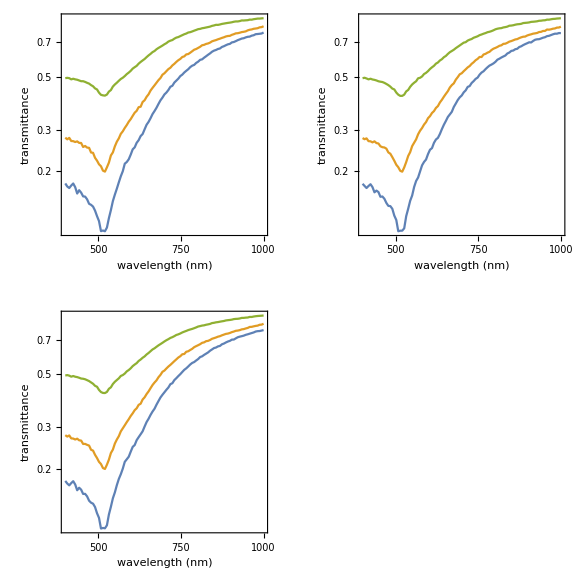

```mathematica
g2=Legended[GraphicsGrid[{{g[[1]],g[[2]]},{g[[3]]}},ImageSize->Large],Placed[LineLegend[Table[ColorData[97,i],{i,3}],{"Target radius = 1.3 μm, thickness = 0.8 μm","Target radius = 1.5 μm, thickness = 0.6 μm","Target radius = 2.0 μm, thickness = 0.3375 μm"},LabelStyle->{13,White}],{0.99,0.1}]]
```

top left to right: E_(||), E_⊥
bottom left: unpolarized incident EM

### Absorbance

```mathematica
data=dat;
Do[data[[All,All,i]]=-Log[10,dat[[All,All,i]]],{i,8,10}];
g=Table[ListPlot[Table[{wav[[j]],data[[i,j,k]]},{i,4,6},{j,1,Length[wav]}],PlotStyle->Table[ColorData[97,i],{i,3}], Frame->True,Axes->False,FrameStyle->Medium,Joined->True,AspectRatio->1,FrameLabel->{"wavelength (nm)","absorbance"},PlotRangePadding->None],{k,8,10}];
```

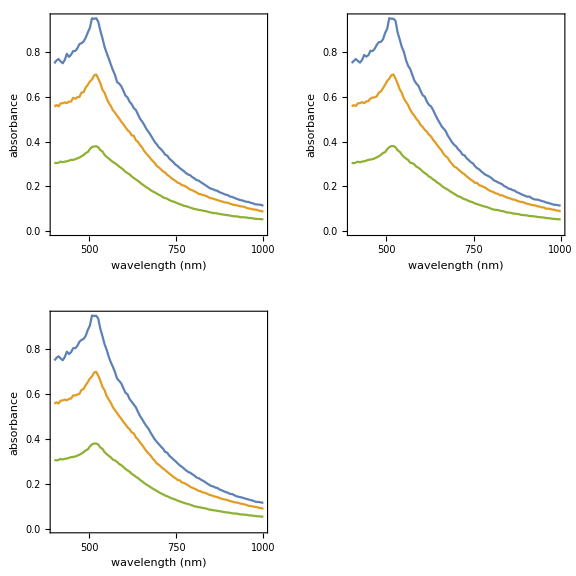

```mathematica
g2=Legended[GraphicsGrid[{{g[[1]],g[[2]]},{g[[3]]}},ImageSize->Large],Placed[LineLegend[Table[ColorData[97,i],{i,3}],{"Target radius = 1.3 μm, thickness = 0.8 μm","Target radius = 1.5 μm, thickness = 0.6 μm","Target radius = 2.0 μm, thickness = 0.3375 μm"},LabelStyle->{13,White}],{0.99,0.1}]]
```

top left to right: E_(||), E_⊥
bottom left: unpolarized incident EM

## Random Configuration

### Reflectance vs wavelength

```mathematica
g=Table[ListLogPlot[Table[{wav[[j]],dat[[i,j,k]]},{i,7,9},{j,1,Length[wav]}],PlotStyle->Table[ColorData[97,i],{i,3}], Frame->True,Axes->False,FrameStyle->Medium,Joined->True,AspectRatio->1,FrameLabel->{"wavelength (nm)","reflectance"},PlotRangePadding->None],{k,2,4}];
```

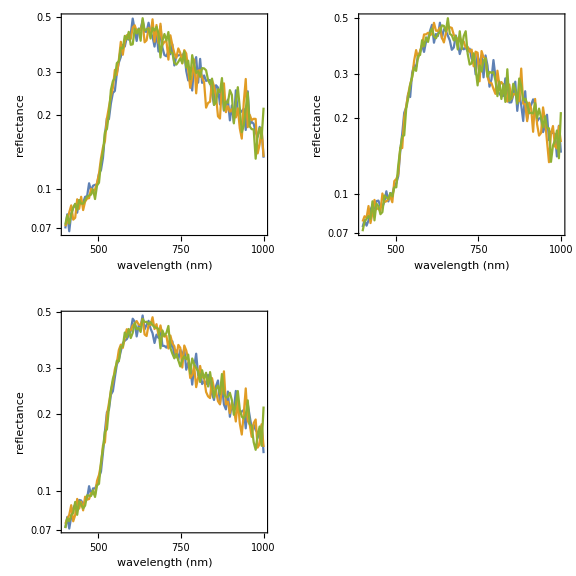

```mathematica
g2=Legended[GraphicsGrid[{{g[[1]],g[[2]]},{g[[3]]}},ImageSize->Large],Placed[LineLegend[Table[ColorData[97,i],{i,3}],{"Configuration A","Configuration B","Configuration C"},LabelStyle->{13,White}],{0.99,0.1}]]
```

top left to right: E_(||), E_⊥
bottom left: unpolarized incident EM

### Absorptance vs wavelength

```mathematica
g=Table[ListLogPlot[Table[{wav[[j]],dat[[i,j,k]]},{i,7,9},{j,1,Length[wav]}],PlotStyle->Table[ColorData[97,i],{i,3}], Frame->True,Axes->False,FrameStyle->Medium,Joined->True,AspectRatio->1,FrameLabel->{"wavelength (nm)","absorptance"},PlotRangePadding->None],{k,5,7}];
```

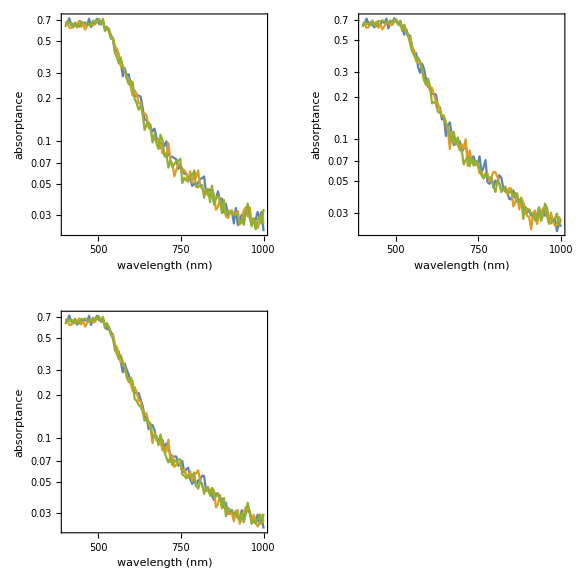

```mathematica
g2=Legended[GraphicsGrid[{{g[[1]],g[[2]]},{g[[3]]}},ImageSize->Large],Placed[LineLegend[Table[ColorData[97,i],{i,3}],{"Configuration A","Configuration B","Configuration C"},LabelStyle->{13,White}],{0.99,0.1}]]
```

top left to right: E_(||), E_⊥
bottom left: unpolarized incident EM

### Transmittance vs wavelength

```mathematica
g=Table[ListLogPlot[Table[{wav[[j]],dat[[i,j,k]]},{i,7,9},{j,1,Length[wav]}],PlotStyle->Table[ColorData[97,i],{i,3}], Frame->True,Axes->False,FrameStyle->Medium,Joined->True,AspectRatio->1,FrameLabel->{"wavelength (nm)","transmittance"},PlotRangePadding->None],{k,8,10}];
```

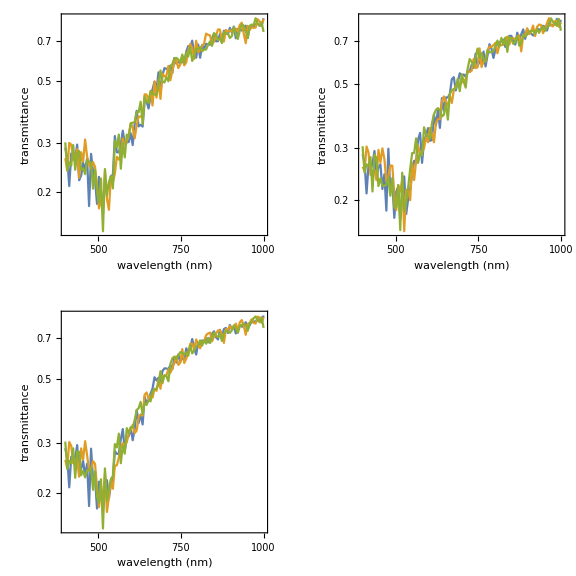

```mathematica
g2=Legended[GraphicsGrid[{{g[[1]],g[[2]]},{g[[3]]}},ImageSize->Large],Placed[LineLegend[Table[ColorData[97,i],{i,3}],{"Configuration A","Configuration B","Configuration C"},LabelStyle->{13,White}],{0.99,0.1}]]
```

top left to right: E_(||), E_⊥
bottom left: unpolarized incident EM

### Absorbance vs wavelength

```mathematica
data=dat;
Do[data[[All,All,i]]=-Log[10,dat[[All,All,i]]],{i,8,10}];
g=Table[ListPlot[Table[{wav[[j]],data[[i,j,k]]},{i,7,9},{j,1,Length[wav]}],PlotStyle->Table[ColorData[97,i],{i,3}], Frame->True,Axes->False,FrameStyle->Medium,Joined->True,AspectRatio->1,FrameLabel->{"wavelength (nm)","absorbance"},PlotRangePadding->None],{k,8,10}];
```

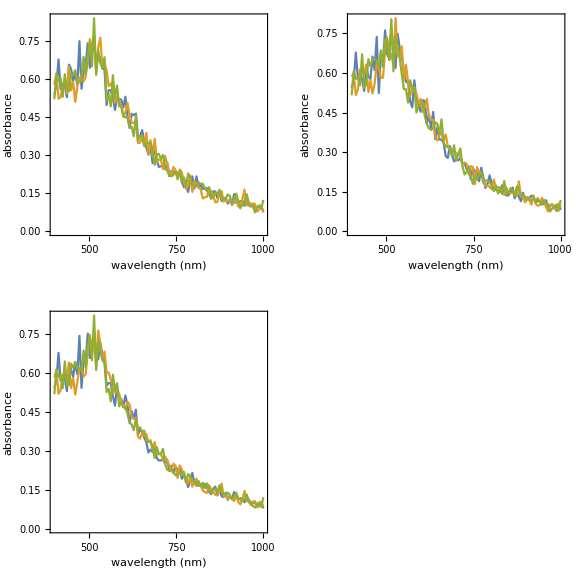

```mathematica
g2=Legended[GraphicsGrid[{{g[[1]],g[[2]]},{g[[3]]}},ImageSize->Large],Placed[LineLegend[Table[ColorData[97,i],{i,3}],{"Configuration A","Configuration B","Configuration C"},LabelStyle->{13,White}],{0.99,0.1}]]
```

top left to right: E_(||), E_⊥
bottom left: unpolarized incident EM

### Reflectance vs incident angle

```mathematica
vars={" incident alpha, beta"," unit cell reflectance"," unit cell reflectance"," unit cell reflectance"," unit cell reflectance"," unit cell reflectance"," unit cell reflectance"," unit cell reflectance"," unit cell reflectance"," unit cell reflectance"};
len={2,4,7,1,5,8,2,6,9,3};
datCAA=readmstm["beer_n_100_a.dat",vars,len];
datCBA=readmstm["beer_n_100_b.dat",vars,len];
datCCA=readmstm["beer_n_100_c.dat",vars,len];
datPNA=readmstm["beer_pyramid_norm.dat",vars,len];
datPIA=readmstm["beer_pyramid_inv.dat",vars,len];
dat={datCAA,datCBA,datCCA,datPNA,datPIA};
```

```mathematica
g=Table[ListLogPlot[Table[{dat[[i,j,1]],dat[[i,j,k]]},{i,1,3},{j,1,Length[dat[[1]]]}],PlotStyle->Table[ColorData[97,i],{i,3}], Frame->True,Axes->False,FrameStyle->Medium,Joined->True,AspectRatio->1,FrameLabel->{"incident angle","reflectance"},PlotRangePadding->None],{k,2,4}];
```

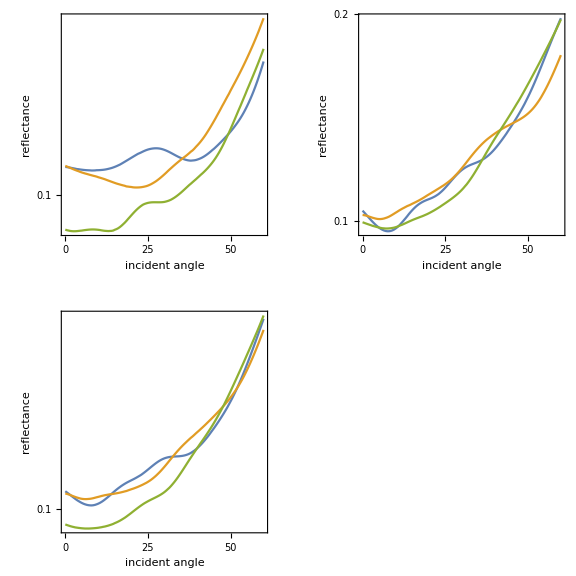

```mathematica
g2=Legended[GraphicsGrid[{{g[[1]],g[[2]]},{g[[3]]}},ImageSize->Large],Placed[LineLegend[Table[ColorData[97,i],{i,3}],{"Configuration A","Configuration B","Configuration C"},LabelStyle->{13,White}],{0.99,0.1}]]
```

top left to right: E_(||), E_⊥
bottom left: unpolarized incident EM

### Absorptance vs incident angle

```mathematica
g=Table[ListLogPlot[Table[{dat[[i,j,1]],dat[[i,j,k]]},{i,1,3},{j,1,Length[dat[[1]]]}],PlotStyle->Table[ColorData[97,i],{i,3}], Frame->True,Axes->False,FrameStyle->Medium,Joined->True,AspectRatio->1,FrameLabel->{"incident angle","absorptance"},PlotRangePadding->None],{k,5,7}];
```

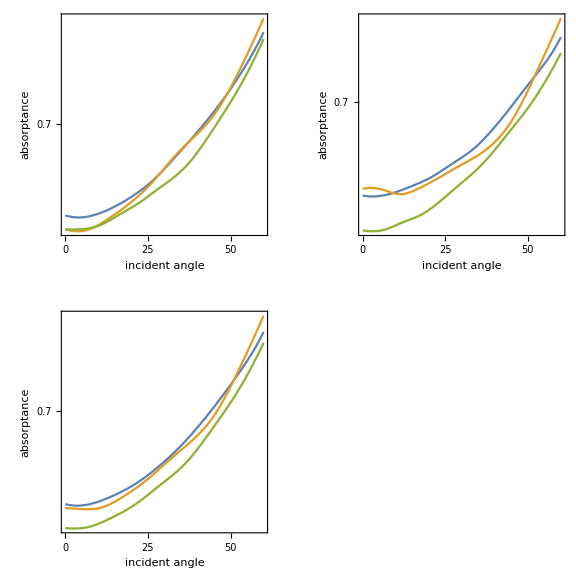

```mathematica
g2=Legended[GraphicsGrid[{{g[[1]],g[[2]]},{g[[3]]}},ImageSize->Large],Placed[LineLegend[Table[ColorData[97,i],{i,3}],{"Configuration A","Configuration B","Configuration C"},LabelStyle->{13,White}],{0.99,0.1}]]
```

top left to right: E_(||), E_⊥
bottom left: unpolarized incident EM

### Transmittance vs incident angle

```mathematica
g=Table[ListLogPlot[Table[{dat[[i,j,1]],dat[[i,j,k]]},{i,1,3},{j,1,Length[dat[[1]]]}],PlotStyle->Table[ColorData[97,i],{i,3}], Frame->True,Axes->False,FrameStyle->Medium,Joined->True,AspectRatio->1,FrameLabel->{"incident angle","transmittance"},PlotRangePadding->None],{k,8,10}];
```

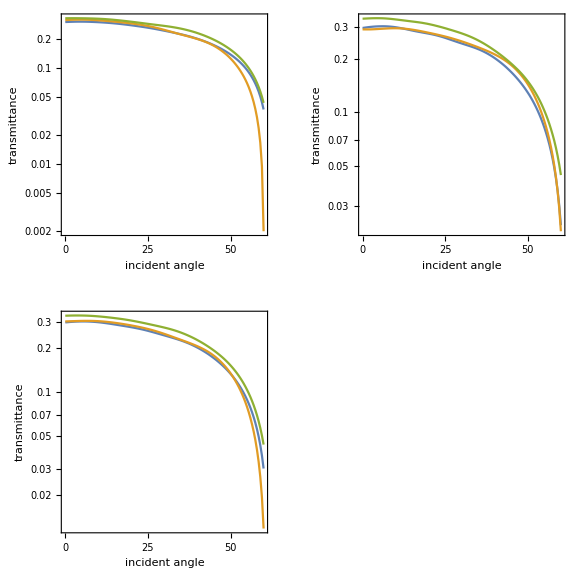

```mathematica
g2=Legended[GraphicsGrid[{{g[[1]],g[[2]]},{g[[3]]}},ImageSize->Large],Placed[LineLegend[Table[ColorData[97,i],{i,3}],{"Configuration A","Configuration B","Configuration C"},LabelStyle->{13,White}],{0.99,0.1}]]
```

top left to right: E_(||), E_⊥
bottom left: unpolarized incident EM

### Absorbance vs incident angle

```mathematica
data=dat;
Do[data[[All,All,i]]=-Log[10,dat[[All,All,i]]],{i,8,10}];
g=Table[ListPlot[Table[{dat[[i,j,1]],data[[i,j,k]]},{i,1,3},{j,1,Length[dat[[1]]]}],PlotStyle->Table[ColorData[97,i],{i,3}], Frame->True,Axes->False,FrameStyle->Medium,Joined->True,AspectRatio->1,FrameLabel->{"incident angle","absorbance"},PlotRangePadding->None],{k,8,10}];
```

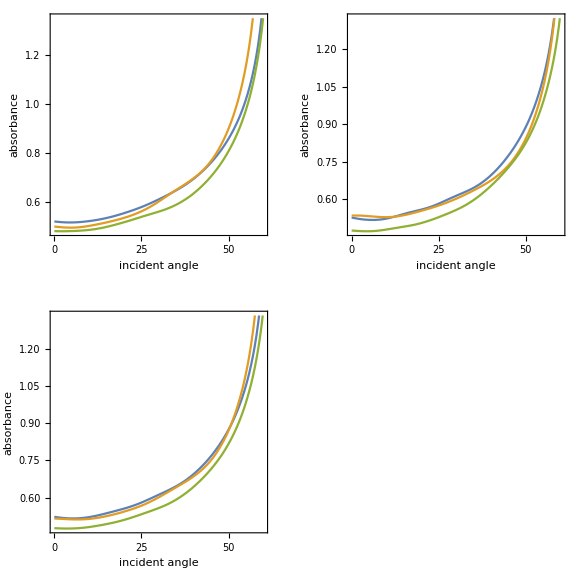

```mathematica
g2=Legended[GraphicsGrid[{{g[[1]],g[[2]]},{g[[3]]}},ImageSize->Large],Placed[LineLegend[Table[ColorData[97,i],{i,3}],{"Configuration A","Configuration B","Configuration C"},LabelStyle->{13,White}],{0.99,0.1}]]
```

top left to right: E_(||), E_⊥
bottom left: unpolarized incident EM

## Distinct Configuration

```mathematica
vars={" length, ref index"," unit cell reflectance"," unit cell reflectance"," unit cell reflectance"," unit cell reflectance"," unit cell reflectance"," unit cell reflectance"," unit cell reflectance"," unit cell reflectance"," unit cell reflectance"};
len={1,4,7,1,5,8,2,6,9,3};
datN050=readmstm["beer_n_050_var.dat",vars,len];
datN100=readmstm["beer_n_100_var.dat",vars,len];
datN150=readmstm["beer_n_150_var.dat",vars,len];
datR13HT4=readmstm["beer_r_13_ht_4_var.dat",vars,len];
datR15HT3=readmstm["beer_r_15_ht_3_var.dat",vars,len];
datR20HT1=readmstm["beer_r_20_ht_1.6875_var.dat",vars,len];
datCA=readmstm["beer_n_100_a_var.dat",vars,len];
datCB=readmstm["beer_n_100_b_var.dat",vars,len];
datCC=readmstm["beer_n_100_c_var.dat",vars,len];
dat1=readmstm["beer_1_var.dat",vars,len];
dat2=readmstm["beer_2_var.dat",vars,len];
dat3=readmstm["beer_3_var.dat",vars,len];
dat4=readmstm["beer_4_var.dat",vars,len];
dat5=readmstm["beer_5_var.dat",vars,len];
dat6=readmstm["beer_6_var.dat",vars,len];
dat7=readmstm["beer_7_var.dat",vars,len];
dat8=readmstm["beer_8_var.dat",vars,len];
dat9=readmstm["beer_9_var.dat",vars,len];
dat={datN050,datN100,datN150,datR13HT4,datR15HT3,datR20HT1,datCA,datCB,datCC,dat1,dat2,dat3,dat4,dat5,dat6,dat7,dat8,dat9};
wav=(2 Pi)/datN050[[All,1]] 0.1 ×1000;
```

### Reflectance vs wavelength

```mathematica
g=Table[ListLogPlot[Table[{wav[[j]],dat[[i,j,k]]},{i,10,18},{j,1,Length[wav]}],PlotStyle->Table[ColorData[97,i],{i,9}], Frame->True,Axes->False,FrameStyle->Medium,Joined->True,AspectRatio->1,FrameLabel->{"wavelength (nm)","reflectance"},PlotRangePadding->None],{k,2,4}];
```

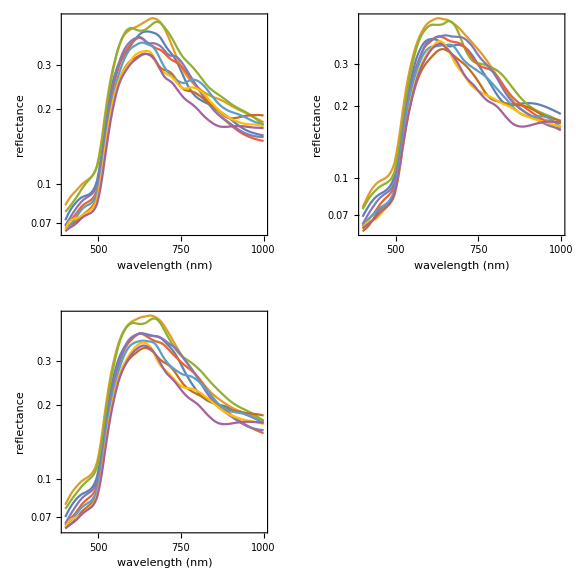

```mathematica
g2=Legended[GraphicsGrid[{{g[[1]],g[[2]]},{g[[3]]}},ImageSize->Large],Placed[LineLegend[Table[ColorData[97,i],{i,9}],{"Configuration 1","Configuration 2","Configuration 3","Configuration 4","Configuration 5","Configuration 6","Configuration 7","Configuration 8","Configuration 9"},LabelStyle->{13,White}],{0.99,0.1}]]
```

top left to right: E_(||), E_⊥
bottom left: unpolarized incident EM

### Absorptance vs wavelength

```mathematica
g=Table[ListLogPlot[Table[{wav[[j]],dat[[i,j,k]]},{i,10,18},{j,1,Length[wav]}],PlotStyle->Table[ColorData[97,i],{i,9}], Frame->True,Axes->False,FrameStyle->Medium,Joined->True,AspectRatio->1,FrameLabel->{"wavelength (nm)","absorptance"},PlotRangePadding->None],{k,5,7}];
```

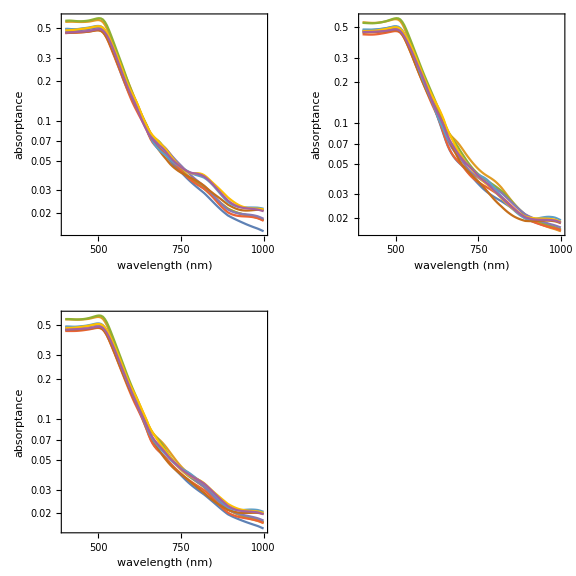

```mathematica
g2=Legended[GraphicsGrid[{{g[[1]],g[[2]]},{g[[3]]}},ImageSize->Large],Placed[LineLegend[Table[ColorData[97,i],{i,9}],{"Configuration 1","Configuration 2","Configuration 3","Configuration 4","Configuration 5","Configuration 6","Configuration 7","Configuration 8","Configuration 9"},LabelStyle->{13,White}],{0.99,0.1}]]
```

top left to right: E_(||), E_⊥
bottom left: unpolarized incident EM

### Transmittance vs wavelength

```mathematica
g=Table[ListLogPlot[Table[{wav[[j]],dat[[i,j,k]]},{i,10,18},{j,1,Length[wav]}],PlotStyle->Table[ColorData[97,i],{i,9}], Frame->True,Axes->False,FrameStyle->Medium,Joined->True,AspectRatio->1,FrameLabel->{"wavelength (nm)","transmittance"},PlotRangePadding->None],{k,8,10}];
```

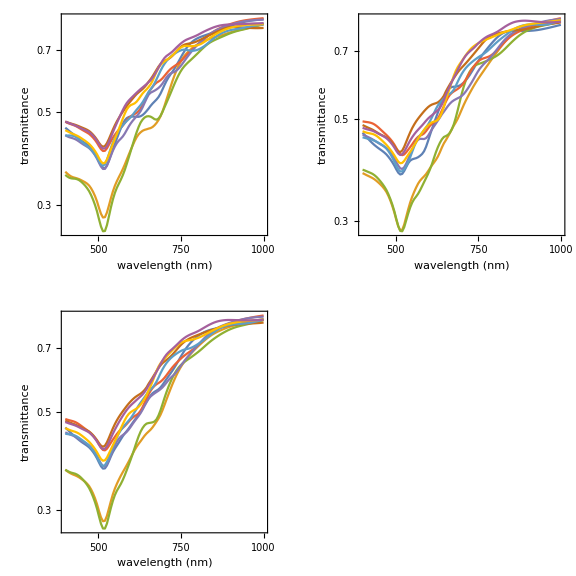

```mathematica
g2=Legended[GraphicsGrid[{{g[[1]],g[[2]]},{g[[3]]}},ImageSize->Large],Placed[LineLegend[Table[ColorData[97,i],{i,9}],{"Configuration 1","Configuration 2","Configuration 3","Configuration 4","Configuration 5","Configuration 6","Configuration 7","Configuration 8","Configuration 9"},LabelStyle->{13,White}],{0.99,0.1}]]
```

top left to right: E_(||), E_⊥
bottom left: unpolarized incident EM

### Absorbance vs wavelength

```mathematica
data=dat;
Do[data[[All,All,i]]=-Log[10,dat[[All,All,i]]],{i,8,10}];
g=Table[ListPlot[Table[{wav[[j]],data[[i,j,k]]},{i,10,18},{j,1,Length[wav]}],PlotStyle->Table[ColorData[97,i],{i,9}], Frame->True,Axes->False,FrameStyle->Medium,Joined->True,AspectRatio->1,FrameLabel->{"wavelength (nm)","absorbance"},PlotRangePadding->None],{k,8,10}];
```

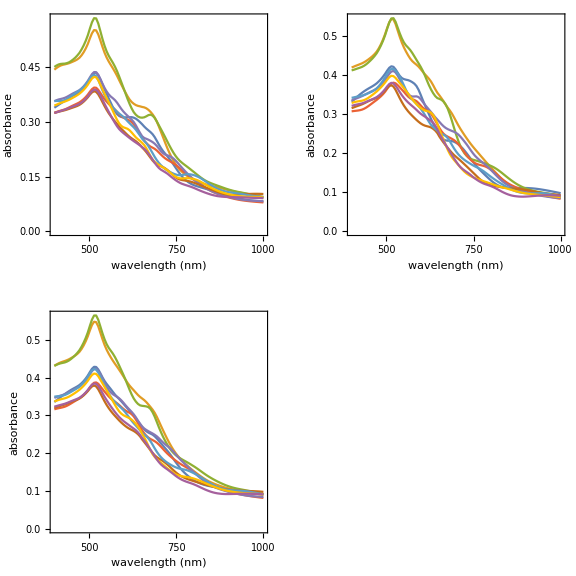

```mathematica
g2=Legended[GraphicsGrid[{{g[[1]],g[[2]]},{g[[3]]}},ImageSize->Large],Placed[LineLegend[Table[ColorData[97,i],{i,9}],{"Configuration 1","Configuration 2","Configuration 3","Configuration 4","Configuration 5","Configuration 6","Configuration 7","Configuration 8","Configuration 9"},LabelStyle->{13,White}],{0.99,0.1}]]
```

top left to right: E_(||), E_⊥
bottom left: unpolarized incident EM

### Reflectance vs incident angle

```mathematica
vars={" incident alpha, beta"," unit cell reflectance"," unit cell reflectance"," unit cell reflectance"," unit cell reflectance"," unit cell reflectance"," unit cell reflectance"," unit cell reflectance"," unit cell reflectance"," unit cell reflectance"};
len={2,4,7,1,5,8,2,6,9,3};
datCAA=readmstm["beer_n_100_a.dat",vars,len];
datCBA=readmstm["beer_n_100_b.dat",vars,len];
datCCA=readmstm["beer_n_100_c.dat",vars,len];
dat1A=readmstm["beer_1.dat",vars,len];
dat2A=readmstm["beer_2.dat",vars,len];
dat3A=readmstm["beer_3.dat",vars,len];
dat4A=readmstm["beer_4.dat",vars,len];
dat5A=readmstm["beer_5.dat",vars,len];
dat6A=readmstm["beer_6.dat",vars,len];
dat7A=readmstm["beer_7.dat",vars,len];
dat8A=readmstm["beer_8.dat",vars,len];
dat9A=readmstm["beer_9.dat",vars,len];
dat={datCAA,datCBA,datCCA,dat1A,dat2A,dat3A,dat4A,dat5A,dat6A,dat7A,dat8A,dat9A};
```

```mathematica
g=Table[ListLogPlot[Table[{dat[[i,j,1]],dat[[i,j,k]]},{i,4,12},{j,1,Length[dat[[4]]]}],PlotStyle->Table[ColorData[97,i],{i,9}], Frame->True,Axes->False,FrameStyle->Medium,Joined->True,AspectRatio->1,FrameLabel->{"incident angle","reflectance"},PlotRangePadding->None],{k,2,4}];
```

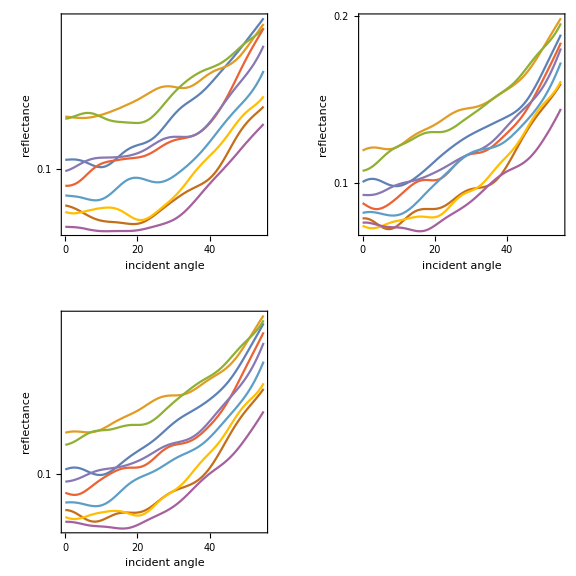

```mathematica
g2=Legended[GraphicsGrid[{{g[[1]],g[[2]]},{g[[3]]}},ImageSize->Large],Placed[LineLegend[Table[ColorData[97,i],{i,9}],{"Configuration 1","Configuration 2","Configuration 3","Configuration 4","Configuration 5","Configuration 6","Configuration 7","Configuration 8","Configuration 9"},LabelStyle->{13,White}],{0.99,0.1}]]
```

top left to right: E_(||), E_⊥
bottom left: unpolarized incident EM

### Absorptance vs incident angle

```mathematica
g=Table[ListLogPlot[Table[{dat[[i,j,1]],dat[[i,j,k]]},{i,4,12},{j,1,Length[dat[[4]]]}],PlotStyle->Table[ColorData[97,i],{i,9}], Frame->True,Axes->False,FrameStyle->Medium,Joined->True,AspectRatio->1,FrameLabel->{"incident angle","absorptance"},PlotRangePadding->None],{k,5,7}];
```

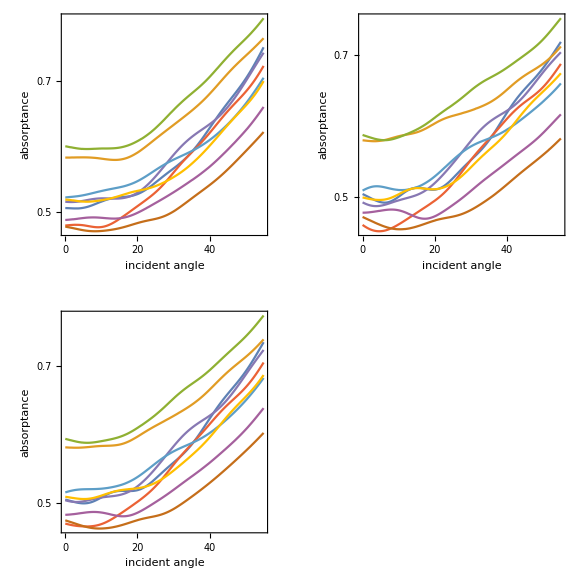

```mathematica
g2=Legended[GraphicsGrid[{{g[[1]],g[[2]]},{g[[3]]}},ImageSize->Large],Placed[LineLegend[Table[ColorData[97,i],{i,9}],{"Configuration 1","Configuration 2","Configuration 3","Configuration 4","Configuration 5","Configuration 6","Configuration 7","Configuration 8","Configuration 9"},LabelStyle->{13,White}],{0.99,0.1}]]
```

top left to right: E_(||), E_⊥
bottom left: unpolarized incident EM

### Transmittance vs incident angle

```mathematica
g=Table[ListLogPlot[Table[{dat[[i,j,1]],dat[[i,j,k]]},{i,4,12},{j,1,Length[dat[[4]]]}],PlotStyle->Table[ColorData[97,i],{i,9}], Frame->True,Axes->False,FrameStyle->Medium,Joined->True,AspectRatio->1,FrameLabel->{"incident angle","transmittance"},PlotRangePadding->None],{k,8,10}];
```

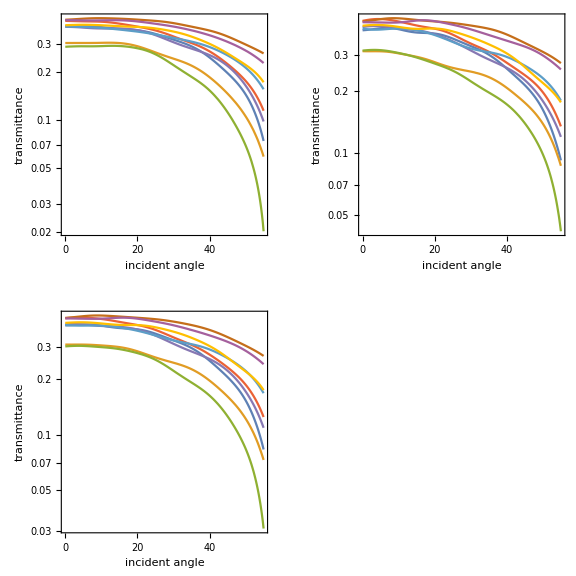

```mathematica
g2=Legended[GraphicsGrid[{{g[[1]],g[[2]]},{g[[3]]}},ImageSize->Large],Placed[LineLegend[Table[ColorData[97,i],{i,9}],{"Configuration 1","Configuration 2","Configuration 3","Configuration 4","Configuration 5","Configuration 6","Configuration 7","Configuration 8","Configuration 9"},LabelStyle->{13,White}],{0.99,0.1}]]
```

top left to right: E_(||), E_⊥
bottom left: unpolarized incident EM

### Absorbance vs incident angle

```mathematica
data=dat;
Do[data[[All,All,i]]=-Log[10,dat[[All,All,i]]],{i,8,10}];
g=Table[ListPlot[Table[{dat[[i,j,1]],data[[i,j,k]]},{i,4,12},{j,1,Length[dat[[4]]]}],PlotStyle->Table[ColorData[97,i],{i,9}], Frame->True,Axes->False,FrameStyle->Medium,Joined->True,AspectRatio->1,FrameLabel->{"incident angle","absorbance"},PlotRangePadding->None],{k,8,10}];
```

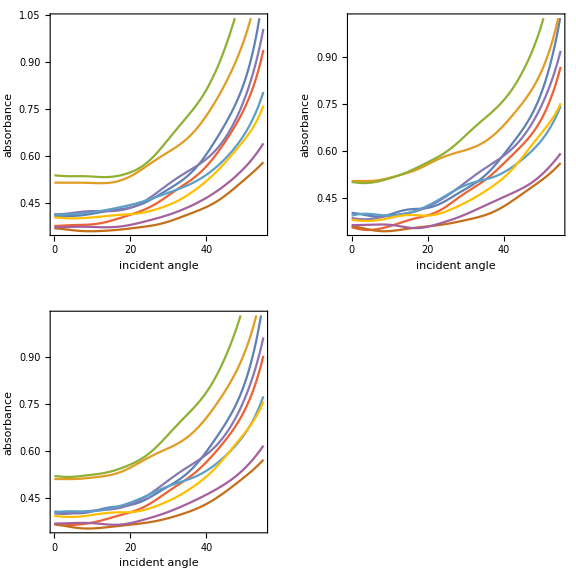

```mathematica
g2=Legended[GraphicsGrid[{{g[[1]],g[[2]]},{g[[3]]}},ImageSize->Large],Placed[LineLegend[Table[ColorData[97,i],{i,9}],{"Configuration 1","Configuration 2","Configuration 3","Configuration 4","Configuration 5","Configuration 6","Configuration 7","Configuration 8","Configuration 9"},LabelStyle->{13,White}],{0.99,0.1}]]
```

top left to right: E_(||), E_⊥
bottom left: unpolarized incident EM